```mathematica
kl[x_, y_] := Piecewise[{{x+y, x<y}, {0, x==y}, {-x-y, y<x}}]
kh[x_, y_] := Piecewise[{{x+y-2, x<y}, {0, x==y}, {2-x-y, y<x}}]
```

```mathematica
Plot3D[kh[1-x,y], {x, 0, 1}, {y, 0, 1}]
```

-Graphics3D-

```mathematica
km[x_, y_]:=FullSimplify[PiecewiseExpand[kl[x,y]+kh[1-x,y]], Assumptions->{0≤x≤1,0≤y≤1}]
km[x, y]
```

Piecewise[{{-1+2 y, x+y>1&&x<y}, {-1-x+y, x+y>1&&x≤y}, {-1-2 x, x+y>1}, {x+y, x+y≥1&&x<y}, {0, x+y≥1&&x≤y}, {-x-y, x+y≥1}, {1+2 x, x<y}, {1+x-y, x≤y}, {1-2 y, True}}]

```mathematica
Plot3D[km[x, y], {x, 0, 1}, {y, 0, 1}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
khalf[y_]:=PiecewiseExpand[kl[1/2, y] + kh[1/2, y]]
```

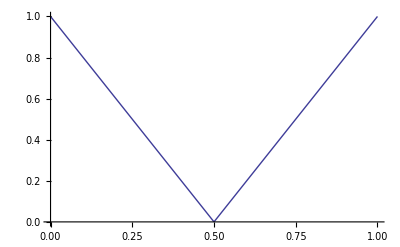

{0,{y→1/2}}

```mathematica
Plot[khalf[y], {y, 0, 1}]
Minimize[khalf[y], {y}]
```

```mathematica
kyhalf[x1_, x2_]:=PiecewiseExpand[kl[x1, 1/2] + kh[x2, 1/2]]
Plot3D[kyhalf[x1, x2], {x1, 0,1},{x2, 0, 1}]
Minimize[{kyhalf[x1, x2],0≤x1≤1 , 0≤x2≤1}, {x1, x2}]
```

-Graphics3D-

{-3,{x1→1,x2→0}}

Plot::exclul: {Max[1 - x - y, -x + y] - 0, Max[x - y, -1 + x + y] - 0, Max[-x + y, -1 + x + y] - 0, Max[-x + y, -1 + x + y] - 0, Max[x - y, -1 + x + y] - 0, Max[1 - x - y, x - y] - 0, Max[x - y, -1 + x + y] - 0, Max[1 - x - y, x - y] - 0, Max[x - y, -1 + x + y] - 0} must be a list of equalities or real-valued functions.

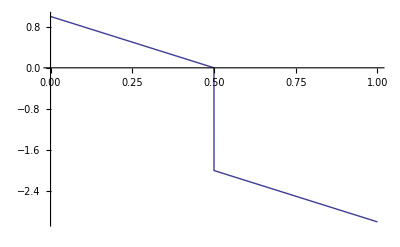

```mathematica
Minimize[{km[x,y], 0≤y≤1}, y][[1]]
```

```mathematica
NDSolve[{4*x*f'[x]+2*f[x]-1==0,f[1]==1},f,{x,0,1}]
```

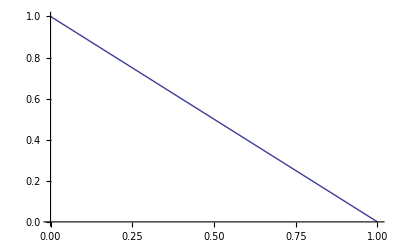

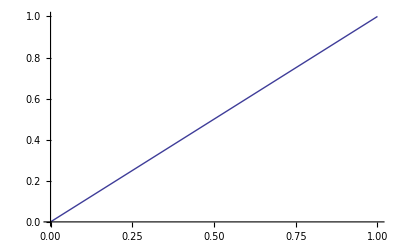

```mathematica
Plot[kh[1,y], {y,0,1}]
Plot[kl[0,y],{y,0,1}]
```

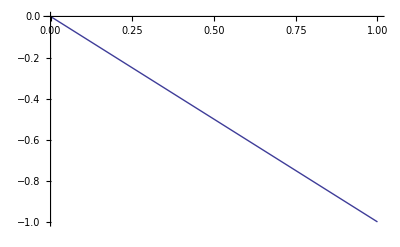

```mathematica
Plot[kl[xl, 0], {xl, 0, 1}]
```

```mathematica
kl[1,1]
```

0

```mathematica
Simplify[kl[0,y]]
Simplify[kh[1,y]]
```

Piecewise[{{-y, y≤0}, {y, True}}]

Piecewise[{{1-y, y≤1}, {-1+y, True}}]

```mathematica
1/2*kl[0,0]+1/2*kl[0,1]+1/2*kh[1,0]+1/2*kh[1,1]
```

1